```mathematica
(*Setting up the problem*) 

Clear ["Global`*"]
```

```mathematica
v0 = 1;
```

```mathematica
(*Setting up potential function*) 
v[x_,α_, λ_] :=v0  α*x^2 

(*Schrodinger equation*)
```

u(x) represents the wavefunction

```mathematica
eqn[en_,α_?NumericQ, λ_?NumericQ] := u''[x] + 2(en - v[x,α, λ])u[x]
```

```mathematica
L = 4;
```

```mathematica
NDSolve[{eqn[1,0.2,0.1]==0, u[-L]==0,u'[-L] == 1}, u, {x, -L, 0} ]
```

{{u→InterpolatingFunction[…]}}

Bounds of the box enclosing the function +/-

Calculate the wavefunction between -L and 0

```mathematica
wavefunc[en_, α_?NumericQ, λ_] := NDSolve[{ eqn[en, α, λ] == 0, u[-L] ==  0, 
					u'[-L] == 1}, u, {x, -L, 0} ]
sol[x_?NumericQ, en_?NumericQ, α_?NumericQ, λ_?NumericQ] := u[x] /.wavefunc[en, α, λ][[1]]
```

Derivative of the wavefunction:

```mathematica
solprime[x_?NumericQ, en_?NumericQ, α_?NumericQ, λ_?NumericQ] := u'[x] /.wavefunc[en,α, λ][[1]]
```

Anharmonic Oscillator:

```mathematica
Clear[v]
```

Pass in variable, x, and parameter coefficients alpha and lambda

```mathematica
v[x_,α_, λ_] := α x^2 + λ x^4
```

Set parameter values

```mathematica
λ = 0.2
α = 0.5
```

0.2

0.5

```mathematica
L = 4
```

4

```mathematica
max = 4;
min = -4;
```

```mathematica
discreteX = 128; (*Number of x values to be evaluated*)
```

```mathematica
divider = (max-min) / (discreteX - 1.0)
```

0.0629921

```mathematica
trainingSize = 500
```

500

```mathematica
testingSize = 100
```

100

```mathematica
increments = Table[i, {i,min, max, divider}];  (*1d table of disctete x values for a given lambda value*)
```

```mathematica
4
(*loop starts here*) 
(*19-23 evaluated once per alpha/lambda value*)
```

4

```mathematica
evalue = en /. FindRoot[solprime[0,en,α,λ],{en,0,1}]
```

0.602405

```mathematica
efunc[x_,α_,λ_] = u[x] /.wavefunc[evalue, α,λ][[1]];
```

```mathematica
ψnn [x_,α_,λ_] := efunc[-x, α,λ] /; x > 0
```

```mathematica
ψnn [x_,α_,λ_] := efunc[x, α,λ] /; x ≤ 0
```

```mathematica
normconst = Sqrt[NIntegrate[ψnn [x,α,λ]^2,{x,-L,L}]];
```

```mathematica
ψ[x_,α_,λ_] := ψnn[x,α,λ]/normconst;
(*evaluate ψ at discrete x values and store as an array and write to disk*)
```

```mathematica
fig = Plot[ψ[x,α,λ],{x,-L,L}, AxesLabel -> {"x","ψ"}];
```

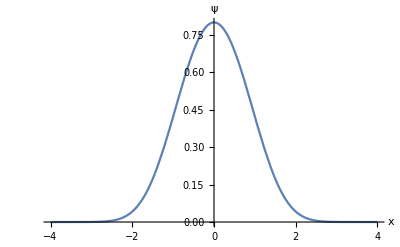

```mathematica
Show[fig]
```

Calculate Evalue: Get first excited even state

```mathematica
evalue = en /. FindRoot[solprime[0,en,α,λ],{en, 2.5,3.5}]
```

FindRoot::lstol: The line search decreased the step size to within tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the merit function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

3.5363

Lowest Odd Eigenstate Calculation:

```mathematica
efunc[x_,α_,λ_] = u[x] /.wavefunc[evalue,α,λ][[1]];
```

```mathematica
normconst = Sqrt[NIntegrate[ψnn[x,α,λ]^2,{x,-L,L}]];
```

```mathematica
evalue = en /. FindRoot[sol[0,en, α,λ],{en,1,2}]
```

1.95054

```mathematica
1.9505435452331785
(*Loop over different values, generate training set with alpha and lambda values*) 
(*New notebook to setup a for loop for alpha and lambda values*) 
(*pass in wavefunction at discrete x values and learn lambda and alpha values *)
(*pick alpha and lambda randomly and choose a set of alpha values and a set of 
lambda values and pick all possible pairs and generate corresponding wavefunction values*) 
(*Each pair of values corresponds to one dataset (a few thousand)*)
(*Generate pairs of alpha lambda values randomly for as many samples as you
want*)
(*pass in wavefunction^2*)
```

1.95054